```mathematica
(*The boson kernell*)
```

```mathematica
m=0.01;
```

```mathematica
points =1000;
domain = {0, 20};
```

```mathematica
f0[x_]:=1/(1+E^(x))
B[x_]:=ArcTan[x/m]/(4Pi)
```

```mathematica
NonLimitIntegrandDiag[w_,wp_]:=B[w+wp](Coth[(w+wp)/2]-Tanh[wp/2])+B[w-wp](Coth[(w-wp)/2]+Tanh[wp/2])
```

```mathematica
LimitIntegrandDiag[w_]=Limit[B[w+wp](Coth[(w+wp)/2]-Tanh[wp/2])+B[w-wp](Coth[(w-wp)/2]+Tanh[wp/2]),wp-> w]
```

0.0795775 Csch[w] (1. ArcTan[200. w]+100. Sech[0.5 w] Sinh[1.5 w]+100. Tanh[0.5 w])

```mathematica
IntegrandDiag[w_,wp_]:=Table[If[w==wp[[i]],LimitIntegrandDiag[w],NonLimitIntegrandDiag[w,wp[[i]]]],{i,points}]/(2Pi)
```

```mathematica
NonDiagIntegrandFerm[w_,wp_]:=B[w+wp](Coth[(w+wp)/2]-Tanh[w/2])-B[w-wp](Coth[(w-wp)/2]-Tanh[w/2])
DiagIntegrandFerm[w_]=Limit[B[w+wp](Coth[(w+wp)/2]-Tanh[w/2])-B[w-wp](Coth[(w-wp)/2]-Tanh[w/2]),wp-> w]
IntegrandFerm[w_,wp_]:=If[w==wp,DiagIntegrandFerm[w],NonDiagIntegrandFerm[w,wp]]/(2 Pi)
```

0.0795775 Csch[w] (1. ArcTan[200. w]-100. Sech[0.5 w] Sinh[1.5 w]-100. Tanh[0.5 w])

```mathematica
IntB[x_,w_,wp_]:=1/(2Pi x)B[x](Tanh[(w+x)/2]+Tanh[(w-x)/2]-2 Tanh[w/2])(Tanh[(wp+x)/2]+Tanh[(wp-x)/2])
```

```mathematica
IntegrandB[w_,wp_]:=NIntegrate[IntB[x,w,wp],{x,0,1000},Exclusions->{0}]
```

```mathematica
(*Computing the calculation basis*)
```

```mathematica
{nodes,weights}=Most[NIntegrate`GaussRuleData[points,MachinePrecision]];
```

```mathematica
midgrid=Rescale[nodes,{0,1},domain];
weightsSK=weights *domain[[2]];
```

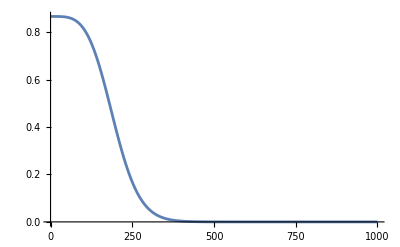

```mathematica
f1=(-D[f0[x],{x,1}]/Sqrt[Integrate[Evaluate[D[f0[y],{y,1}]]^2,{y,0,Infinity}]])/.{x->midgrid};
ListLinePlot[f1, PlotRange->All]
NumIntegrate[x_,y_]:=Total[weightsSK*x*y]
WIntegrate[x_,y_]:=Total[weightsSK*(f1^2)*x*y]
WIntegrate3[x_,A_,y_]:=Total[x*f1*weightsSK*(A.(f1 * y *weightsSK))]
```

```mathematica
ClearAll[TestFN,TestFNUnnorm]
```

```mathematica
X=midgrid;
```

```mathematica
TestFNUnnorm[n_Integer]:=TestFNUnnorm[n]=FullSimplify[(X^2 * TestFN[n-1]-Evaluate[Sum[TestFN[i]*WIntegrate[TestFN[i],X^2*TestFN[n-1]],{i,n-1}]])]
TestFN[n_Integer]:=TestFN[n]=TestFNUnnorm[n]/Sqrt[WIntegrate[TestFNUnnorm[n],TestFNUnnorm[n]]]
TestFN[1]:=X/Sqrt[WIntegrate[X,X]]
```

```mathematica
Nb=6;
Basis=Table[TestFN[n],{n,Nb}];
```

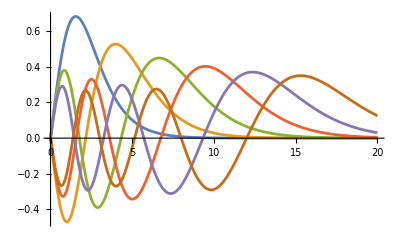

```mathematica
ListLinePlot[Table[Transpose[{midgrid,Basis[[i]]*f1}],{i,Nb}]]
```

```mathematica
Table[WIntegrate[Basis[[i]],Basis[[j]]],{i,Nb},{j,Nb}]
```

{{1.,1.80478×10^-16,-2.03074×10^-16,2.16824×10^-16,-2.14631×10^-16,1.92861×10^-16},{1.80478×10^-16,1.,2.90922×10^-17,-3.01805×10^-17,3.41133×10^-17,-2.10036×10^-17},{-2.03074×10^-16,2.90922×10^-17,1.,-2.49177×10^-16,1.43076×10^-16,-9.98721×10^-17},{2.16824×10^-16,-3.01805×10^-17,-2.49177×10^-16,1.,-3.27223×10^-16,2.23315×10^-16},{-2.14631×10^-16,3.41133×10^-17,1.43076×10^-16,-3.27223×10^-16,1.,5.44704×10^-16},{1.92861×10^-16,-2.10036×10^-17,-9.98721×10^-17,2.23315×10^-16,5.44704×10^-16,1.}}

```mathematica
(*Computing the matrix elements of operators*)
```

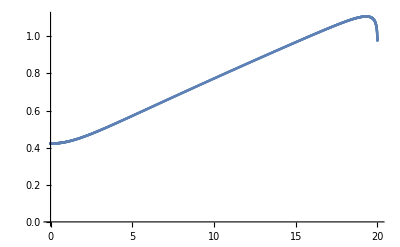

```mathematica
g=Table [NumIntegrate[IntegrandDiag[X[[i]],X],ConstantArray[1, points]],{i,points}];
ListPlot[Transpose[{midgrid,g}]]
```

```mathematica
gdelf=Table[WIntegrate[Basis[[i]],g*Basis[[j]]],{i,Nb},{j,Nb}]
```

{{0.459334,0.029506,-0.00485707,0.00171548,-0.000808526,0.000448291},{0.029506,0.525074,0.0575237,-0.011201,0.00440518,-0.00224239},{-0.00485707,0.0575237,0.600499,0.0850354,-0.0176581,0.00730477},{0.00171548,-0.011201,0.0850354,0.678142,0.111542,-0.024013},{-0.000808526,0.00440518,-0.0176581,0.111542,0.755297,0.136442},{0.000448291,-0.00224239,0.00730477,-0.024013,0.136442,0.825232}}

```mathematica
{vals, vecs}=Eigensystem[gdelf];
```

```mathematica
vals
```

{0.942283,0.776408,0.651635,0.55427,0.481946,0.437035}

```mathematica
(*Operator is completely positive, makes sense*)
```

```mathematica
vecs[[4]]
```

{-0.204494,-0.720615,-0.133925,0.443232,-0.407182,0.2423}

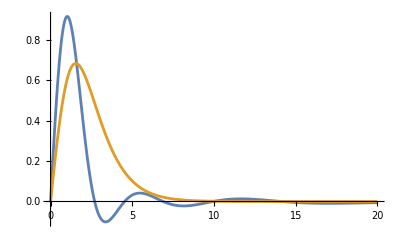

```mathematica
eigvecsg=vecs.Basis;
ListLinePlot[{Table[Transpose[{midgrid,eigvecsg[[i]]*f1}],{i,Nb}][[6]],Table[Transpose[{midgrid,Basis[[i]]*f1}],{i,Nb}][[1]]},PlotRange->All]
```

```mathematica
KerIg=Table[IntegrandFerm[X[[i]],X[[j]]],{i,points},{j,points}];
```

```mathematica
NonDiagF=Table[WIntegrate3[Basis[[i]],KerIg,Basis[[j]]],{i,Nb},{j,Nb}]
```

{{-0.391342,-0.124003,-0.102331,-0.10795,-0.103126,-0.0917234},{-0.018387,-0.395795,-0.145326,-0.113043,-0.120326,-0.101316},{0.00351217,-0.0194783,-0.398594,-0.149808,-0.110334,-0.109349},{-0.00131487,0.00497398,-0.0193194,-0.399467,-0.147545,-0.0953022},{0.000640093,-0.00220156,0.0057038,-0.0181653,-0.396026,-0.132367},{-0.000362302,0.00120893,-0.00268005,0.0065523,-0.01385,-0.380089}}

```mathematica
ColIntEq = gdelf+NonDiagF;
```

```mathematica
{vals,vecseq}=Eigensystem[ColIntEq];
Min[Re[vals]]
```

0.0807257

```mathematica
vals*(4 Pi)
```

{5.25225+0.955581 ⅈ,5.25225-0.955581 ⅈ,2.72978+0.575133 ⅈ,2.72978-0.575133 ⅈ,1.64817,1.01443}

```mathematica
(*m=0.1, correction:0.98
m=0.01, correction:1.01*)
```

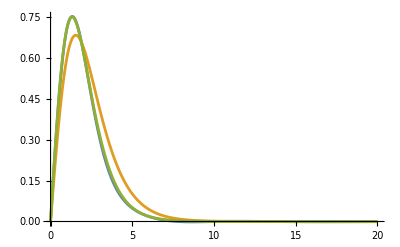

```mathematica
(*Comparing the eigenmode to expected eigenmode from analytics for thermalized boson - blue vs green curve, great conversion*)
eigvecseq=vecseq.Basis;
ListLinePlot[{Table[Transpose[{midgrid,Re[eigvecseq[[i]]*f1]}],{i,Nb}][[6]],Table[Transpose[{midgrid,Basis[[i]]*f1}],{i,Nb}][[1]],Transpose[{midgrid,2.25Tanh[X/2]*f1}]},PlotRange->All]
```

```mathematica
(*Incorporating the boson*)
```

```mathematica
ClearAll[x]
```

```mathematica
Monitor[KerIb=Table[IntegrandB[X[[i]],X[[j]]],{i,points},{j,points}],ProgressIndicator[i,{0,points}]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {22.9467}. NIntegrate obtained -0.0241239 and 1.888×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {22.9467}. NIntegrate obtained -0.0242108 and 1.85904×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {22.9467}. NIntegrate obtained -0.024032 and 1.95649×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Collision_Integral_SM.mx"}],KerIb]
```

C:\Users\Serhii Kryhin\Dropbox (Harvard University)\non-linear transport\Paper backups\PRL_v4\Git data\Collision_Integral_SM.mx

```mathematica
KerIb=Import[FileNameJoin[{NotebookDirectory[],"Collision_Integral_SM.mx"}]]
```

```mathematica
Ib=Table[WIntegrate3[Basis[[i]],KerIb,Basis[[j]]],{i,Nb},{j,Nb}]
gdelf+NonDiagF
ColIntEq = gdelf+NonDiagF+ Ib
```

{{-0.0679918,-0.154597,-0.244938,-0.31177,-0.350851,-0.338675},{-0.011119,-0.0488985,-0.115916,-0.186158,-0.234947,-0.240486},{0.00134493,-0.00290193,-0.0280127,-0.076997,-0.126577,-0.146119},{-0.000400593,-4.27243×10^-7,-0.00271162,-0.020954,-0.0559772,-0.082239},{0.000168442,0.0000729981,0.000352242,-0.00137921,-0.0137351,-0.0336918},{-0.0000859844,-0.0000522399,-0.000106859,0.000232483,-0.000089793,-0.00573644}}

{{0.0679919,-0.0944967,-0.107189,-0.106235,-0.103934,-0.0912751},{0.011119,0.129278,-0.0878026,-0.124244,-0.115921,-0.103558},{-0.0013449,0.0380453,0.201905,-0.0647721,-0.127992,-0.102044},{0.000400604,-0.00622702,0.0657161,0.278674,-0.0360021,-0.119315},{-0.000168433,0.00220362,-0.0119543,0.0933772,0.359271,0.0040749},{0.0000859889,-0.00103346,0.00462472,-0.0174607,0.122592,0.445143}}

{{5.33619×10^-8,-0.249093,-0.352127,-0.418005,-0.454785,-0.429951},{1.68354×10^-9,0.0803796,-0.203719,-0.310402,-0.350868,-0.344044},{3.09778×10^-8,0.0351434,0.173893,-0.141769,-0.25457,-0.248163},{1.13885×10^-8,-0.00622745,0.0630044,0.25772,-0.0919793,-0.201554},{9.90616×10^-9,0.00227662,-0.0116021,0.091998,0.345536,-0.0296169},{4.52153×10^-9,-0.0010857,0.00451786,-0.0172282,0.122502,0.439406}}

```mathematica
{vals,vecsb}=Eigensystem[ColIntEq];
Min[Re[vals]];
```

```mathematica
vals
```

{0.405367+0.116522 ⅈ,0.405367-0.116522 ⅈ,0.192895+0.0810436 ⅈ,0.192895-0.0810436 ⅈ,0.100408,2.76796×10^-7}

```mathematica
(*0-eigenvalue eigenmode profile, proportional to the T-derivative of a Fermi function - pure heating*)
```

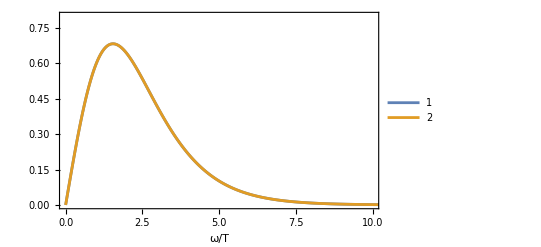

```mathematica
eigvecsb=vecsb.Basis;
ListLinePlot[{Table[Transpose[{midgrid,Re[eigvecsb[[i]]*f1]}],{i,Nb}][[6]],Table[Transpose[{midgrid,Basis[[i]]*f1}],{i,Nb}][[1]]},PlotRange->{{0,10},{0,0.8}},Frame->True,Axes->False,PlotLegends->Automatic,FrameLabel->{"ω/T"},LabelStyle->{FontFamily->"CMU Serif",FontSize->14}]
```

```mathematica
(*Constructing conjugate functional basis*)
```

```mathematica
Conjugate[vecsb[[1]]].vecsb[[6]]
```

-0.248437-0.00313544 ⅈ

```mathematica
Matr=Table[Conjugate[vecsb[[i]]].vecsb[[j]],{i,Nb},{j,Nb}];
Matr//MatrixForm
```

(1.+0. ⅈ | 0.188234+0.165708 ⅈ | -0.340478-0.155919 ⅈ | -0.0178467+0.0616412 ⅈ | -0.128943+0.0690669 ⅈ | -0.248437-0.00313544 ⅈ
0.188234-0.165708 ⅈ | 1.+0. ⅈ | -0.0178467-0.0616412 ⅈ | -0.340478+0.155919 ⅈ | -0.128943-0.0690669 ⅈ | -0.248437+0.00313544 ⅈ
-0.340478+0.155919 ⅈ | -0.0178467+0.0616412 ⅈ | 1.+0. ⅈ | -0.15116+0.0471332 ⅈ | -0.283586-0.395411 ⅈ | -0.0320871-0.539049 ⅈ
-0.0178467-0.0616412 ⅈ | -0.340478-0.155919 ⅈ | -0.15116-0.0471332 ⅈ | 1.+0. ⅈ | -0.283586+0.395411 ⅈ | -0.0320871+0.539049 ⅈ
-0.128943-0.0690669 ⅈ | -0.128943+0.0690669 ⅈ | -0.283586+0.395411 ⅈ | -0.283586-0.395411 ⅈ | 1.+0. ⅈ | 0.883061+0. ⅈ
-0.248437+0.00313544 ⅈ | -0.248437-0.00313544 ⅈ | -0.0320871+0.539049 ⅈ | -0.0320871-0.539049 ⅈ | 0.883061+0. ⅈ | 1.+0. ⅈ)

```mathematica
Inverse[Matr]//MatrixForm
```

(3.4364-2.66454×10^-15 ⅈ | -2.108-1.04507 ⅈ | 4.50818-3.12675 ⅈ | -2.31893-4.45249 ⅈ | 2.81829-12.664 ⅈ | -2.80637+14.3778 ⅈ
-2.108+1.04507 ⅈ | 3.4364-1.77636×10^-15 ⅈ | -2.31893+4.45249 ⅈ | 4.50818+3.12675 ⅈ | 2.81829+12.664 ⅈ | -2.80637-14.3778 ⅈ
4.50818+3.12675 ⅈ | -2.31893-4.45249 ⅈ | 13.8696-1.06581×10^-14 ⅈ | 2.64554-11.5608 ⅈ | 24.9488-19.192 ⅈ | -27.2131+22.3191 ⅈ
-2.31893+4.45249 ⅈ | 4.50818-3.12675 ⅈ | 2.64554+11.5608 ⅈ | 13.8696-1.59872×10^-14 ⅈ | 24.9488+19.192 ⅈ | -27.2131-22.3191 ⅈ
2.81829+12.664 ⅈ | 2.81829-12.664 ⅈ | 24.9488+19.192 ⅈ | 24.9488-19.192 ⅈ | 82.3783-1.10539×10^-13 ⅈ | -90.5139+1.23568×10^-13 ⅈ
-2.80637-14.3778 ⅈ | -2.80637+14.3778 ⅈ | -27.2131-22.3191 ⅈ | -27.2131+22.3191 ⅈ | -90.5139+1.23568×10^-13 ⅈ | 101.941-1.3815×10^-13 ⅈ)

```mathematica
ebasis=vecsb.Basis;
```

```mathematica
fbasis=Conjugate[Inverse[Matr]].vecsb.Basis;
```

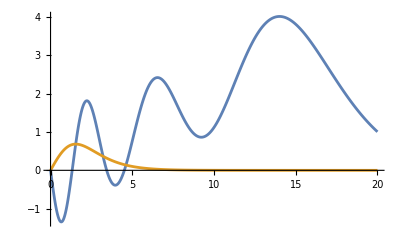

```mathematica
ListLinePlot[{Table[Transpose[{midgrid,Re[fbasis[[i]]*f1]}],{i,Nb}][[6]],Table[Transpose[{midgrid,Re[ebasis[[i]]*f1]}],{i,Nb}][[6]]},PlotRange->All]
```

```mathematica
WIntegrate[Conjugate[fbasis[[6]]],ebasis[[6]]]
```

1.+3.12494×10^-16 ⅈ

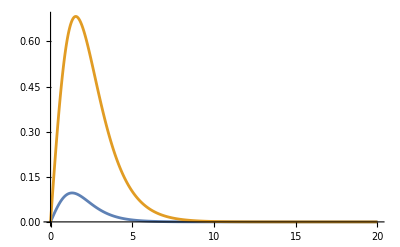

```mathematica
f2=Evaluate[D[f0[x],{x,2}]]/.{x->X};
ListLinePlot[{Transpose[{midgrid,f2}],Table[Transpose[{midgrid,Basis[[i]]*f1}],{i,Nb}][[1]]},PlotRange->All]
```

```mathematica
Total[weightsSK*f1*fbasis[[6]]*f2]*8*Sqrt[2]
```

0.99941+2.58819×10^-15 ⅈ

```mathematica
(*Analytic expression for the basis function*)
```

```mathematica
basisf6=x D[f0[x],x]/Sqrt[Integrate[(x D[f0[y],y]/.{y->x})^2,{x,0,Infinity}]]
```

-(6 ⅇ^x x)/((1+ⅇ^x)^2 √(-6+π^2))

```mathematica
(*Combining 1/8 Sqrt[2] and 6/Sqrt[pi^2 -6] results in A_cr in Eq. 108*)
```

```mathematica
Integrate[basisf6^2,{x,0,Infinity}]
```

1

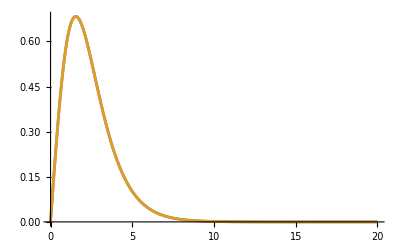

```mathematica
ListLinePlot[{Transpose[{midgrid,-basisf6/.{x->X}}],Table[Transpose[{midgrid,Re[ebasis[[i]]*f1]}],{i,Nb}][[6]]},PlotRange->All]
```